## Definition

## Definition

## Definition

```mathematica
ClearAll[FindRandomMazeSolution]
```

#### Main Definition

```mathematica
FindRandomMazeSolution[{m1_?{{-Graphics-, PositiveIntegerQ}} /;!(m1<=1),n1_?{{-Graphics-, PositiveIntegerQ}}/;!(n1<=1)}]:=Module[{g,maze,m,solvedmaze,shortestPath,start,end,shortestPathSubgraph,tree},g=GridGraph[{m1,n1}];m=Graph[VertexList[g],Module[{stack={RandomChoice[VertexList[g]]}},
Do[AnnotationValue[{g,v},"Visited"]=False,{v,VertexList[g]}];
AnnotationValue[{g,First@stack},"Visited"]=True;
While[Not[stack=={}],
With[{v=First@stack},
With[{adj=Cases[EdgeList[g,v<->_]/.{v<->u_:>u,u_<->v:>u},x_/;¬AnnotationValue[{g,x},"Visited"]]},
If[adj=={},
stack=Rest@stack,
With[{w=RandomChoice[adj]},
PrependTo[stack,w];
AnnotationValue[{g,w},"Visited"]=True;
Sow[v<->w]]]]]]]//Reap//Last//First, VertexCoordinates->GraphEmbedding[g]];maze=m;
start=1(*First@VertexList[m]*);end=m1*n1(*Last@VertexList[m]*) (*We are only removing edges, not vertices. The last vertex will always be the product of m and n.*);solvedmaze=HighlightGraph[m,PathGraph@(shortestPath=FindShortestPath[m,start,end])];tree=GraphTree[maze];shortestPathSubgraph=Subgraph[maze,shortestPath];<|"maze"->maze,"solved-maze"->solvedmaze,"shortest-path"->shortestPath,"distance"->GraphDistance[m,start,end],"start"->start,"end"->end,"shortest-path-subgraph"->shortestPathSubgraph,"tree"->tree|>]
FindRandomMazeSolution[{m1_?{{-Graphics-, PositiveIntegerQ}} /;!(m1<=1),n1_?{{-Graphics-, PositiveIntegerQ}}/;!(n1<=1)},property_/;MatchQ[property,(Alternatives@@{"maze","solved-maze","shortest-path","distance","start","end","shortest-path-subgraph"})]]:=Lookup[FindRandomMazeSolution[{m1,n1}],property]
FindRandomMazeSolution[{m1_?{{-Graphics-, PositiveIntegerQ}} /;!(m1<=1),n1_?{{-Graphics-, PositiveIntegerQ}}/;!(n1<=1)},property_?VectorQ]:=AssociationMap[p↦Lookup[FindRandomMazeSolution[{m1,n1}],p]][Intersection[{"maze","solved-maze","shortest-path","distance","start","end","shortest-path-subgraph"},property]]
```

#### specify start and end

```mathematica
FindRandomMazeSolution[{m1_?{{-Graphics-, PositiveIntegerQ}} /;!(m1<=1),n1_?{{-Graphics-, PositiveIntegerQ}}/;!(n1<=1)},start_,end_]:=Module[{g,maze,m,solvedmaze,shortestPath,shortestPathSubgraph},g=GridGraph[{m1,n1}];m=Graph[VertexList[g],Module[{stack={RandomChoice[VertexList[g]]}},
Do[AnnotationValue[{g,v},"Visited"]=False,{v,VertexList[g]}];
AnnotationValue[{g,First@stack},"Visited"]=True;
While[Not[stack=={}],
With[{v=First@stack},
With[{adj=Cases[EdgeList[g,v<->_]/.{v<->u_:>u,u_<->v:>u},x_/;¬AnnotationValue[{g,x},"Visited"]]},
If[adj=={},
stack=Rest@stack,
With[{w=RandomChoice[adj]},
PrependTo[stack,w];
AnnotationValue[{g,w},"Visited"]=True;
Sow[v<->w]]]]]]]//Reap//Last//First, VertexCoordinates->GraphEmbedding[g]];maze=m;
solvedmaze=HighlightGraph[m,PathGraph@(shortestPath=FindShortestPath[m,start,end])];shortestPathSubgraph=Subgraph[maze,shortestPath];<|"maze"->maze,"solved-maze"->solvedmaze,"shortest-path"->shortestPath,"distance"->GraphDistance[m,start,end],"start"->start,"end"->end,"shortest-path-subgraph"->shortestPathSubgraph|>]
FindRandomMazeSolution[{m1_?{{-Graphics-, PositiveIntegerQ}} /;!(m1<=1),n1_?{{-Graphics-, PositiveIntegerQ}}/;!(n1<=1)},start_,end_,property_/;MatchQ[property,(Alternatives@@{"maze","solved-maze","shortest-path","distance","start","end","shortest-path-subgraph"})]]:=Lookup[FindRandomMazeSolution[{m1,n1},start,end],property]
FindRandomMazeSolution[{m1_?{{-Graphics-, PositiveIntegerQ}} /;!(m1<=1),n1_?{{-Graphics-, PositiveIntegerQ}}/;!(n1<=1)},start_,end_,property_?VectorQ]:=AssociationMap[p↦Lookup[FindRandomMazeSolution[{m1,n1},start,end],p]][Intersection[{"maze","solved-maze","shortest-path","distance","start","end","shortest-path-subgraph"},property]]
```

#### an antipodal maze

```mathematica
FindRandomMazeSolution[{m1_?{{-Graphics-, PositiveIntegerQ}} /;!(m1<=1),n1_?{{-Graphics-, PositiveIntegerQ}}/;!(n1<=1)},"Antipodal"]:=Module[{g,maze,highlightedStartEnd,m,solvedmaze,shortestPath,shortestPathSubgraph,start,end},g=GridGraph[{m1,n1}];m=Graph[VertexList[g],Module[{stack={RandomChoice[VertexList[g]]}},
Do[AnnotationValue[{g,v},"Visited"]=False,{v,VertexList[g]}];
AnnotationValue[{g,First@stack},"Visited"]=True;
While[Not[stack=={}],
With[{v=First@stack},
With[{adj=Cases[EdgeList[g,v<->_]/.{v<->u_:>u,u_<->v:>u},x_/;¬AnnotationValue[{g,x},"Visited"]]},
If[adj=={},
stack=Rest@stack,
With[{w=RandomChoice[adj]},
PrependTo[stack,w];
AnnotationValue[{g,w},"Visited"]=True;
Sow[v<->w]]]]]]]//Reap//Last//First, VertexCoordinates->GraphEmbedding[g]];maze=m;
{start,end}=ResourceFunction["GraphAntipodes"][m];solvedmaze=HighlightGraph[m,PathGraph@(shortestPath=FindShortestPath[m,start,end])];highlightedStartEnd=HighlightGraph[maze,{start,end}];shortestPathSubgraph=Subgraph[maze,shortestPath];<|"maze"->highlightedStartEnd,"solved-maze"->solvedmaze,"shortest-path"->shortestPath,"distance"->GraphDistance[m,start,end],"start"->start,"end"->end,"shortest-path-subgraph"->shortestPathSubgraph|>]
FindRandomMazeSolution[{m1_?{{-Graphics-, PositiveIntegerQ}} /;!(m1<=1),n1_?{{-Graphics-, PositiveIntegerQ}}/;!(n1<=1)},"Antipodal",property_/;MatchQ[property,(Alternatives@@{"maze","solved-maze","shortest-path","distance","start","end","shortest-path-subgraph"})]]:=Lookup[FindRandomMazeSolution[{m1,n1},"Antipodal"],property]
FindRandomMazeSolution[{m1_?{{-Graphics-, PositiveIntegerQ}} /;!(m1<=1),n1_?{{-Graphics-, PositiveIntegerQ}}/;!(n1<=1)},start_,end_,property_?VectorQ]:=AssociationMap[p↦Lookup[FindRandomMazeSolution[{m1,n1},"Antipodal"],p]][Intersection[{"maze","solved-maze","shortest-path","distance","start","end","shortest-path-subgraph"},property]]
```

#### Triangular Main Definition

```mathematica
FindRandomMazeSolution[m1_?{{-Graphics-, PositiveIntegerQ}} /;!(m1<=0),"Triangular"]:=Module[{g,maze,m,solvedmaze,shortestPath,start,end,shortestPathSubgraph},g=ResourceFunction["TriangularGridGraph"][m1];m=Graph[VertexList[g],Module[{stack={RandomChoice[VertexList[g]]}},
Do[AnnotationValue[{g,v},"Visited"]=False,{v,VertexList[g]}];
AnnotationValue[{g,First@stack},"Visited"]=True;
While[Not[stack=={}],
With[{v=First@stack},
With[{adj=Cases[EdgeList[g,v<->_]/.{v<->u_:>u,u_<->v:>u},x_/;¬AnnotationValue[{g,x},"Visited"]]},
If[adj=={},
stack=Rest@stack,
With[{w=RandomChoice[adj]},
PrependTo[stack,w];
AnnotationValue[{g,w},"Visited"]=True;
Sow[v<->w]]]]]]]//Reap//Last//First, VertexCoordinates->GraphEmbedding[g]];maze=m;
start=1(*First@VertexList[m]*);end=Last[VertexList[g]];solvedmaze=HighlightGraph[m,PathGraph@(shortestPath=FindShortestPath[m,start,end])];shortestPathSubgraph=Subgraph[maze,shortestPath];<|"maze"->maze,"solved-maze"->solvedmaze,"shortest-path"->shortestPath,"distance"->GraphDistance[m,start,end],"start"->start,"end"->end,"shortest-path-subgraph"->shortestPathSubgraph|>]
FindRandomMazeSolution[m1_?{{-Graphics-, PositiveIntegerQ}} /;!(m1<=0),"Triangular",property_/;MatchQ[property,(Alternatives@@{"maze","solved-maze","shortest-path","distance","start","end","shortest-path-subgraph"})]]:=Lookup[FindRandomMazeSolution[m1,"Triangular",property]]
FindRandomMazeSolution[m1_?{{-Graphics-, PositiveIntegerQ}} /;!(m1<=0),"Triangular",property_?VectorQ]:=AssociationMap[p↦Lookup[FindRandomMazeSolution[m1,"Triangular"],p]][Intersection[{"maze","solved-maze","shortest-path","distance","start","end","shortest-path-subgraph"},property]]
```

#### specify start and end

```mathematica
FindRandomMazeSolution[m1_?{{-Graphics-, PositiveIntegerQ}} /;!(m1<=0),"Triangular",start_,end_]:=Module[{g,maze,m,solvedmaze,shortestPath,shortestPathSubgraph},g=ResourceFunction["TriangularGridGraph"][m1];m=Graph[VertexList[g],Module[{stack={RandomChoice[VertexList[g]]}},
Do[AnnotationValue[{g,v},"Visited"]=False,{v,VertexList[g]}];
AnnotationValue[{g,First@stack},"Visited"]=True;
While[Not[stack=={}],
With[{v=First@stack},
With[{adj=Cases[EdgeList[g,v<->_]/.{v<->u_:>u,u_<->v:>u},x_/;¬AnnotationValue[{g,x},"Visited"]]},
If[adj=={},
stack=Rest@stack,
With[{w=RandomChoice[adj]},
PrependTo[stack,w];
AnnotationValue[{g,w},"Visited"]=True;
Sow[v<->w]]]]]]]//Reap//Last//First, VertexCoordinates->GraphEmbedding[g]];maze=m;
solvedmaze=HighlightGraph[m,PathGraph@(shortestPath=FindShortestPath[m,start,end])];shortestPathSubgraph=Subgraph[maze,shortestPath];<|"maze"->maze,"solved-maze"->solvedmaze,"shortest-path"->shortestPath,"distance"->GraphDistance[m,start,end],"start"->start,"end"->end,"shortest-path-subgraph"->shortestPathSubgraph|>]
FindRandomMazeSolution[m1_?{{-Graphics-, PositiveIntegerQ}} /;!(m1<=0),"Triangular",start_,end_,property_/;MatchQ[property,(Alternatives@@{"maze","solved-maze","shortest-path","distance","start","end","shortest-path-subgraph"})]]:=Lookup[FindRandomMazeSolution[m1,"Triangular",property]]
FindRandomMazeSolution[m1_?{{-Graphics-, PositiveIntegerQ}} /;!(m1<=0),"Triangular",start_,end_,property_?VectorQ]:=AssociationMap[p↦Lookup[FindRandomMazeSolution[m1,"Triangular",start,end],p]][Intersection[{"maze","solved-maze","shortest-path","distance","start","end","shortest-path-subgraph"},property]]
```

#### an antipodal maze

```mathematica
FindRandomMazeSolution[m1_?{{-Graphics-, PositiveIntegerQ}} /;!(m1<=0),"Triangular","Antipodal"]:=Module[{g,maze,m,solvedmaze,shortestPath,start,end,shortestPathSubgraph},g=ResourceFunction["TriangularGridGraph"][m1];m=Graph[VertexList[g],Module[{stack={RandomChoice[VertexList[g]]}},
Do[AnnotationValue[{g,v},"Visited"]=False,{v,VertexList[g]}];
AnnotationValue[{g,First@stack},"Visited"]=True;
While[Not[stack=={}],
With[{v=First@stack},
With[{adj=Cases[EdgeList[g,v<->_]/.{v<->u_:>u,u_<->v:>u},x_/;¬AnnotationValue[{g,x},"Visited"]]},
If[adj=={},
stack=Rest@stack,
With[{w=RandomChoice[adj]},
PrependTo[stack,w];
AnnotationValue[{g,w},"Visited"]=True;
Sow[v<->w]]]]]]]//Reap//Last//First, VertexCoordinates->GraphEmbedding[g]];maze=m;
{start,end}=ResourceFunction["GraphAntipodes"][m];solvedmaze=HighlightGraph[m,PathGraph@(shortestPath=FindShortestPath[m,start,end])];shortestPathSubgraph=Subgraph[maze,shortestPath];<|"maze"->maze,"solved-maze"->solvedmaze,"shortest-path"->shortestPath,"distance"->GraphDistance[m,start,end],"start"->start,"end"->end,"shortest-path-subgraph"->shortestPathSubgraph|>]
FindRandomMazeSolution[m1_?{{-Graphics-, PositiveIntegerQ}} /;!(m1<=0),"Triangular","Antipodal",property_/;MatchQ[property,(Alternatives@@{"maze","solved-maze","shortest-path","distance","start","end","shortest-path-subgraph"})]]:=Lookup[FindRandomMazeSolution[m1,"Triangular","Antipodal"],property]
FindRandomMazeSolution[m1_?{{-Graphics-, PositiveIntegerQ}} /;!(m1<=0),"Triangular",property_?VectorQ]:=AssociationMap[p↦Lookup[FindRandomMazeSolution[m1,"Triangular","Antipodal"],p]][Intersection[{"maze","solved-maze","shortest-path","distance","start","end","shortest-path-subgraph"},property]]
```

#### Hexagonal Main Definition

```mathematica
FindRandomMazeSolution[{m1_?{{-Graphics-, PositiveIntegerQ}} /;!(m1<=1),n1_?{{-Graphics-, PositiveIntegerQ}}/;!(n1<=1)},"Hexagonal"]:=Module[{g,maze,m,solvedmaze,shortestPath,start,end,shortestPathSubgraph},g=ResourceFunction["HexagonalGridGraph"][{m1,n1}];m=Graph[VertexList[g],Module[{stack={RandomChoice[VertexList[g]]}},
Do[AnnotationValue[{g,v},"Visited"]=False,{v,VertexList[g]}];
AnnotationValue[{g,First@stack},"Visited"]=True;
While[Not[stack=={}],
With[{v=First@stack},
With[{adj=Cases[EdgeList[g,v<->_]/.{v<->u_:>u,u_<->v:>u},x_/;¬AnnotationValue[{g,x},"Visited"]]},
If[adj=={},
stack=Rest@stack,
With[{w=RandomChoice[adj]},
PrependTo[stack,w];
AnnotationValue[{g,w},"Visited"]=True;
Sow[v<->w]]]]]]]//Reap//Last//First, VertexCoordinates->GraphEmbedding[g]];maze=m;
start=1(*First@VertexList[m]*);end=Last[VertexList[g]];solvedmaze=HighlightGraph[m,PathGraph@(shortestPath=FindShortestPath[m,start,end])];shortestPathSubgraph=Subgraph[maze,shortestPath];<|"maze"->maze,"solved-maze"->solvedmaze,"shortest-path"->shortestPath,"distance"->GraphDistance[m,start,end],"start"->start,"end"->end,"shortest-path-subgraph"->shortestPathSubgraph|>]
```

## Testing

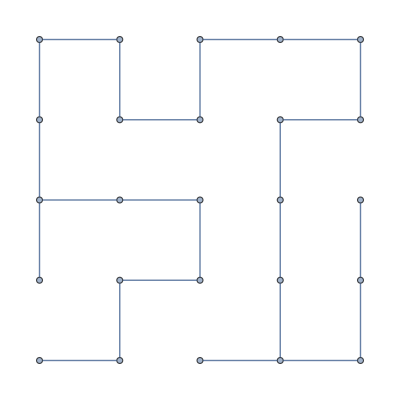
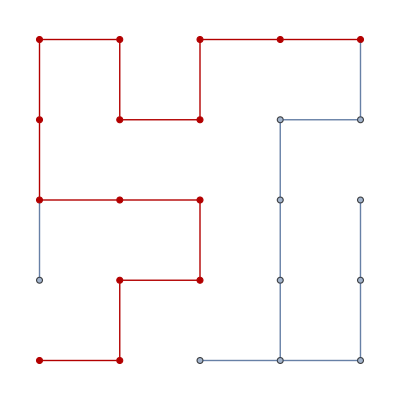
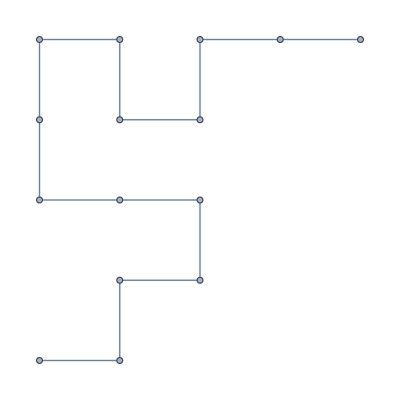
<|maze→-Graphics-,solved-maze→-Graphics-,shortest-path→{1,6,7,12,13,8,3,4,5,10,9,14,15,20,25},distance→14,start→1,end→25,shortest-path-subgraph→-Graphics-,tree→-Graphics-|>

```mathematica
FindRandomMazeSolution[{5,5}]
```

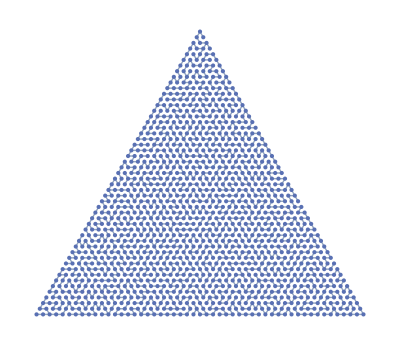
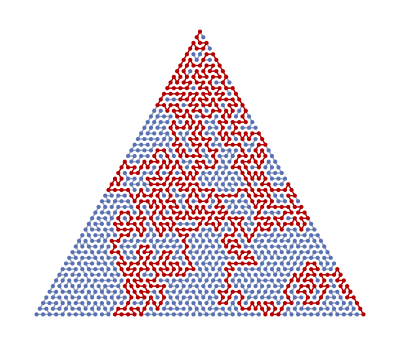
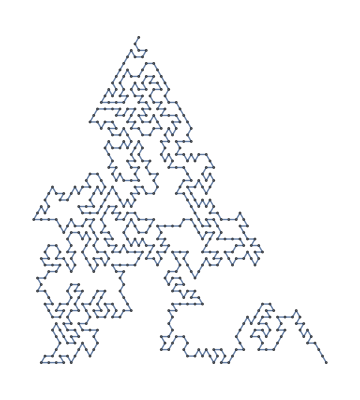
<|maze→-Graphics-,solved-maze→-Graphics-,shortest-path→{1,2,5,6,9,8,4,7,11,16,22,29,38,47,37,46,56,57,58,59,49,48,39,30,23,17,24,25,19,14,15,21,28,36,45,54,65,66,78,91,105,120,135,152,151,150,168,186,187,207,188,208,189,190,210,231,230,251,274,252,275,298,322,297,273,296,295,320,346,373,347,374,348,375,402,403,432,433,434,406,435,465,464,495,527,528,560,561,595,594,629,664,628,593,627,626,661,625,590,591,558,559,526,525,524,523,492,461,431,430,460,459,429,400,372,345,319,318,294,271,272,249,227,226,225,205,185,204,184,166,148,149,132,117,133,118,103,104,90,89,88,76,75,64,63,52,43,44,35,34,27,26,33,42,41,32,40,50,51,61,62,74,73,86,85,99,100,87,101,116,115,130,129,113,112,98,97,84,72,71,83,82,70,69,68,67,79,92,93,108,94,95,110,109,125,126,111,127,144,161,143,160,159,141,158,177,197,217,218,239,262,240,263,264,265,242,221,220,199,200,180,162,145,163,181,201,202,222,244,245,267,291,315,314,289,288,313,312,338,364,337,363,336,310,285,309,334,360,387,386,385,357,358,359,332,307,283,308,284,260,237,236,258,282,281,305,280,304,329,328,303,302,277,301,326,353,380,352,379,407,408,409,410,440,471,441,412,442,443,414,415,444,475,507,539,573,574,609,644,608,607,643,679,642,606,571,538,506,474,505,473,472,503,536,569,570,604,640,676,639,603,602,568,534,533,566,601,600,636,637,638,674,673,710,709,748,787,788,829,871,870,913,957,958,915,914,872,873,832,791,752,753,792,793,833,874,917,916,959,1004,1003,1049,1050,1097,1096,1144,1143,1095,1048,1002,1047,1094,1142,1190,1239,1238,1288,1289,1290,1291,1240,1241,1292,1242,1193,1145,1194,1244,1195,1147,1099,1053,1052,1051,1005,1006,962,918,875,876,835,795,796,836,877,920,919,963,964,921,878,879,922,965,966,923,924,881,839,798,759,720,683,682,645,646,647,648,613,579,578,577,543,576,575,542,541,508,509,477,476,446,416,388,361,362,389,390,418,419,391,392,421,422,423,452,482,481,450,420,449,479,511,544,512,545,513,546,547,580,614,615,651,616,581,582,549,548,516,515,484,453,454,455,456,427,428,458,489,521,490,491,522,554,587,588,589,623,624,659,658,622,657,693,730,692,655,619,585,584,583,618,654,690,689,726,765,727,728,767,766,805,806,847,807,808,848,849,891,890,889,888,887,930,929,973,1017,1063,1109,1108,1156,1204,1205,1157,1110,1111,1159,1207,1257,1258,1209,1259,1210,1260,1311,1261,1211,1212,1262,1312,1313,1263,1214,1215,1166,1118,1072,1027,983,1028,984,941,899,900,943,942,986,985,1029,1030,1076,1122,1075,1074,1120,1121,1169,1217,1218,1219,1171,1124,1078,1077,1032,987,988,989,946,990,1034,1035,1080,1127,1081,1128,1175,1176,1225,1275,1326},distance→610,start→1,end→1326,shortest-path-subgraph→-Graphics-|>

```mathematica
FindRandomMazeSolution[50,"Triangular"]
```

```mathematica
FindRandomMazeSolution[{5,5},"shortest-path"]
```

{1,6,11,16,17,22,23,24,19,18,13,14,15,20,25}

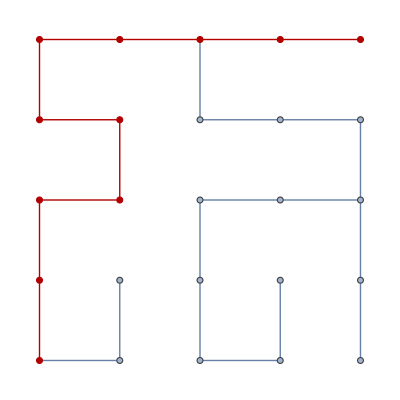
<|shortest-path→{1,2,3,8,7,12,17,18,13,14,15,20,25},solved-maze→-Graphics-|>

```mathematica
FindRandomMazeSolution[{5,5},{"solved-maze","shortest-path"}]
```

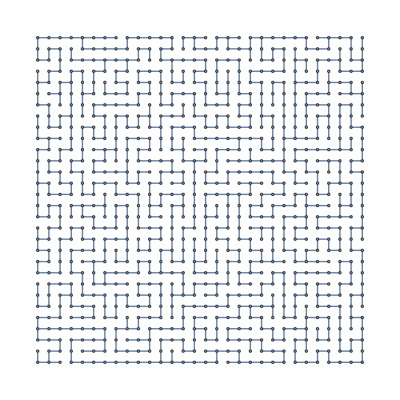
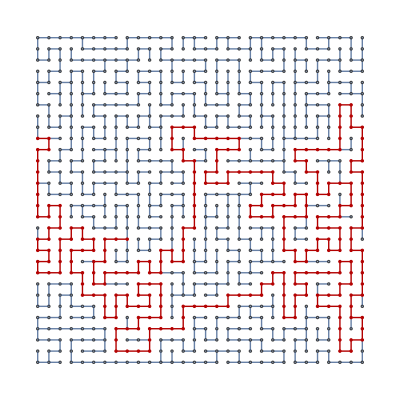
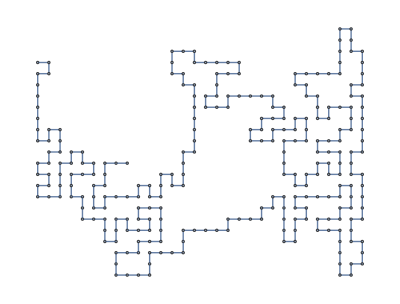
<|maze→-Graphics-,solved-maze→-Graphics-,shortest-path→{21,51,50,20,19,18,17,16,15,14,44,45,75,74,73,43,42,12,11,41,40,10,9,39,69,70,71,72,102,103,133,132,162,161,131,101,100,99,129,128,127,157,187,186,185,215,216,217,247,246,276,306,307,277,278,308,338,337,336,335,305,275,274,244,214,213,212,242,272,302,303,304,334,364,394,395,396,426,456,486,516,517,547,577,607,608,638,639,669,668,667,666,665,695,696,697,727,728,698,699,729,759,789,819,820,850,849,848,818,817,787,757,756,786,816,815,814,813,812,842,843,873,874,875,845,846,847,877,878,879,880,881,851,852,853,883,884,885,886,887,888,858,859,889,890,891,892,862,863,864,834,833,832,831,830,800,770,740,710,709,739,738,768,767,766,796,797,827,857,856,855,825,824,794,764,763,793,823,822,821,791,792,762,761,731,730,700,701,671,672,673,674,704,734,735,736,706,705,675,645,644,614,584,585,615,616,646,676,677,647,648,618,588,558,528,527,497,467,468,498,499,500,530,560,561,531,501,471,441,442,412,382,381,380,410,409,439,438,437,436,435,434,433,403,402,401,400,370,371,341,340,339,309,310,280,279,249,219,189,188,158,159,160,190,191,192,222,252},distance→267,start→21,end→252,shortest-path-subgraph→-Graphics-|>

```mathematica
FindRandomMazeSolution[{30,30},21,400-148]
```

```mathematica
GraphTree[FindRandomMazeSolution[{30,30},"solved-maze"]]
```

-Graphics-

## Hexagonal Graph

```mathematica
MatchQ[{"maze","solved-maze","shortest-path","distance","start","end","shortest-path-subgraph"},property_/;MatchQ[property,(ContainsOnly[{"maze","solved-maze","shortest-path","distance","start","end","shortest-path-subgraph"}][property])]]
```

False

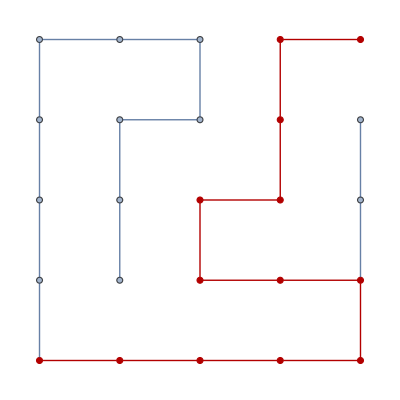
<|shortest-path→{1,6,11,16,17,18,19,24,25},solved-maze→-Graphics-|>

```mathematica
FindRandomMazeSolution[{5,5},{"solved-maze","shortest-path"}]
```

```mathematica
AssessmentFunction[{{1,2,3,4,5,10,15,20,25}}][{1,2,3,4,5,10,15,20,25}]
```

AssessmentResultObject[…]

```mathematica
AssessmentFunction[{{1,2,3,4,5,10,15,20,25}}][{1,2,3,4,5,10,15,20,25}]
```

AssessmentResultObject[…]

```mathematica
AssessmentFunction[{1}][1]
```

AssessmentResultObject[…]

```mathematica
AssessmentFunction[{1}][2]
```

AssessmentResultObject[…]

```mathematica
AssessmentFunction[{1-><|"Score"->1,"AnswerCorrect"->True|>,Except[1]-><|"Score"->0,"AnswerCorrect"->False,"Explanation"->"The correct answer was 1"|>}][2]
```

AssessmentResultObject[…]

```mathematica
AssessmentFunction[{1-><|"Score"->1,"AnswerCorrect"->True|>,Except[1]-><|"Score"->0,"AnswerCorrect"->False,"Explanation"->"The correct answer was 1"|>}][2][All]
```

<|Score→0,MaxScore→1,MinScore→0,AnswerCorrect→False,GivenAnswer→2,Explanation→The correct answer was 1,Timestamp→Mon 19 Jun 2023 16:03:28GMT-4,AssessmentOptions→{},AnswerComparisonMethod→Item|>

```mathematica
AssessmentFunction[{1-><|"Score"->1,"AnswerCorrect"->True|>,Except[1]-><|"Score"->0,"AnswerCorrect"->False,"Explanation"->"The correct answer was 1"|>}][1]
```

AssessmentResultObject[…]

```mathematica
AssessmentFunction[{1-><|"Score"->1,"AnswerCorrect"->True|>,Except[1]-><|"Score"->0,"AnswerCorrect"->False,"Explanation"->"The correct answer was 1"|>}][1][All]
```

<|Score→1,MaxScore→1,MinScore→0,AnswerCorrect→True,GivenAnswer→1,Explanation→None,Timestamp→Mon 19 Jun 2023 16:03:44GMT-4,AssessmentOptions→{},AnswerComparisonMethod→Item|>

```mathematica
QuestionObject[QuestionInterface["ShortAnswer",<|"Prompt"->"What is the next step?",
"Range"->{1,900}|>],AssessmentFunction[{1-><|"Score"->1,"AnswerCorrect"->True|>,Except[1]-><|"Score"->0,"AnswerCorrect"->False,"Explanation"->"The correct answer was 1"|>}]]
```

```mathematica
QuestionObject[QuestionInterface["ShortAnswer",<|"Prompt"->"What is the next step?",
"Range"->{1,900}|>],AssessmentFunction[{1-><|"Score"->1,"AnswerCorrect"->True|>,Except[1]-><|"Score"->0,"AnswerCorrect"->False,"Explanation"->"The correct answer was 1"|>}]]
```

```mathematica
ResourceFunction["QuestionDeploy"][QuestionObject[QuestionInterface["ShortAnswer",<|"Prompt"->"What is the next step?",
"Range"->{1,900}|>],AssessmentFunction[{1-><|"Score"->1,"AnswerCorrect"->True|>,Except[1]-><|"Score"->0,"AnswerCorrect"->False,"Explanation"->"The correct answer was 1"|>}]]]
```

<|QuestionObject→,CloudObject→CloudObject[https://www.wolframcloud.com/obj/2b508366-b30f-4d00-98a5-ae123c0f028d],Website→CloudObject[https://www.wolframcloud.com/obj/2b508366-b30f-4d00-98a5-ae123c0f028d/index.nb]|>

```mathematica
shortestPath={1,2,3,4,5,10,15,20,25};
```

```mathematica
Table[QuestionObject[QuestionInterface["ShortAnswer",<|"Prompt"->"What is the next step?",
"Range"->{1,900}|>],AssessmentFunction[{answer-><|"Score"->1,"AnswerCorrect"->True|>,Except[answer]-><|"Score"->0,"AnswerCorrect"->False,"Explanation"->TemplateApply["The correct answer was `answer`",<|"answer"->answer|>]|>}]],{answer,shortestPath}]
```

{,,,,,,,,}

```mathematica
QuestionDeploy[]
```

```mathematica
nb=CreateDocument[];
```

```mathematica
NotebookWrite[nb,Cell["New content","Subsection"]]
```

```mathematica
NotebookWrite[nb,Cell["Next cell","Subsection"],All]
```

```mathematica
NotebookWrite[nb,Cell[BoxData[FrameBox[RowBox[{"QuestionObject","[",RowBox[{"\"\<XXXX\>\"",",",RowBox[{"MatchQ","[","\"\<XXXX\>\"","]"}]}],"]"}],Alignment->{Left,Top},BaselinePosition->Baseline,FrameStyle->RGBColor[0.7490196078431373,0.7490196078431373,0.7490196078431373],ImageSize->{Scaled[1],{80,800}},RoundingRadius->5,StripOnInput->False]],"FormElementCode",TaggingRules->{"FormNotebook"->{"Type"->"Default","Mode"->"CODE","FormExpr"->RowBox[{"QuestionObject","[",RowBox[{"\"XXXX\"",",",RowBox[{"MatchQ","[","\"XXXX\"","]"}]}],"]"}]}}],All]
```

```mathematica
questionNotebook=CreateNotebook["QuestionNotebook"]
```

```mathematica
NotebookWrite[questionNotebook,Cell[BoxData[FrameBox[RowBox[{"QuestionObject","[",RowBox[{"\"\<XXXX\>\"",",",RowBox[{"MatchQ","[","\"\<XXXX\>\"","]"}]}],"]"}],Alignment->{Left,Top},BaselinePosition->Baseline,FrameStyle->RGBColor[0.7490196078431373,0.7490196078431373,0.7490196078431373],ImageSize->{Scaled[1],{80,800}},RoundingRadius->5,StripOnInput->False]],"FormElementCode",TaggingRules->{"FormNotebook"->{"Type"->"Default","Mode"->"CODE","FormExpr"->RowBox[{"QuestionObject","[",RowBox[{"\"XXXX\"",",",RowBox[{"MatchQ","[","\"XXXX\"","]"}]}],"]"}]}}]]
```

```mathematica
InputForm[QuestionObject[QuestionInterface["ShortAnswer",<|"Prompt"->"What is the next step?",
"Range"->{1,900}|>],AssessmentFunction[{1-><|"Score"->1,"AnswerCorrect"->True|>,Except[1]-><|"Score"->0,"AnswerCorrect"->False,"Explanation"->"The correct answer was 1"|>}]]]
```

QuestionObject[QuestionInterface["ShortAnswer", 
  <|"Prompt" -> "What is the next step?", 
   "Range" -> {1, 900}|>], AssessmentFunction[
  {1 -> <|"Score" -> 1, "AnswerCorrect" -> True|>, 
   Except[1] -> <|"Score" -> 0, "AnswerCorrect" -> False, 
     "Explanation" -> "The correct answer was 1"|>}, 
  <|"ComparisonMethod" -> "Item"|>, "Validated" -> True]]

```mathematica
NotebookWrite[questionNotebook,Cell[BoxData[FrameBox[RowBox[{"QuestionObject","[",RowBox[{"\"\<XXXX\>\"",",",RowBox[{"MatchQ","[","\"\<XXXX\>\"","]"}]}],"]"}],Alignment->{Left,Top},BaselinePosition->Baseline,FrameStyle->RGBColor[0.7490196078431373,0.7490196078431373,0.7490196078431373],ImageSize->{Scaled[1],{80,800}},RoundingRadius->5,StripOnInput->False]],"FormElementCode",TaggingRules->{"FormNotebook"->{"Type"->"Default","Mode"->"CODE","FormExpr"->QuestionObject[QuestionInterface["ShortAnswer",<|"Prompt"->"What is the next step?",
"Range"->{1,900}|>],AssessmentFunction[{1-><|"Score"->1,"AnswerCorrect"->True|>,Except[1]-><|"Score"->0,"AnswerCorrect"->False,"Explanation"->"The correct answer was 1"|>}]]}}]]
```

```mathematica
newQuestionNotebook=CreateNotebook["QuestionNotebook"]
```

```mathematica
NotebookPut[Notebook[{Cell["Replacement content.","Subsection"]}],newQuestionNotebook]
```

```mathematica
SelectionMove[questionNotebook,After,Notebook]
```

```mathematica
NotebookWrite[questionNotebook,Cell[BoxData[FrameBox[RowBox[{"QuestionObject","[",RowBox[{RowBox[{"QuestionInterface","[",RowBox[{"\"\<ShortAnswer\>\"",",",RowBox[{"<|",RowBox[{RowBox[{"\"\<Prompt\>\"","->","\"\<What is the next step?\>\""}],",","
",RowBox[{"\"\<Range\>\"","->",RowBox[{"{",RowBox[{"1",",","900"}],"}"}]}]}],"|>"}]}],"]"}],",",RowBox[{"AssessmentFunction","[",RowBox[{"{",RowBox[{RowBox[{"1","→",RowBox[{"<|",RowBox[{RowBox[{"\"\<Score\>\"","→","1"}],",",RowBox[{"\"\<AnswerCorrect\>\"","→","True"}]}],"|>"}]}],",",RowBox[{RowBox[{"Except","[","1","]"}],"→",RowBox[{"<|",RowBox[{RowBox[{"\"\<Score\>\"","→","0"}],",",RowBox[{"\"\<AnswerCorrect\>\"","→","False"}],",",RowBox[{"\"\<Explanation\>\"","→","\"\<The correct answer was 1\>\""}]}],"|>"}]}]}],"}"}],"]"}]}],"]"}],Alignment->{Left,Top},BaselinePosition->Baseline,FrameStyle->RGBColor[0.7490196078431373,0.7490196078431373,0.7490196078431373],ImageSize->{Scaled[1],{80,800}},RoundingRadius->5,StripOnInput->False]],"FormElementCode",TaggingRules->{"FormNotebook"->{"Type"->"Default","Mode"->"CODE","FormExpr"->RowBox[{"QuestionObject","[",RowBox[{RowBox[{"QuestionInterface","[",RowBox[{"\"ShortAnswer\"",",",RowBox[{"<|",RowBox[{RowBox[{"\"Prompt\"","->","\"What is the next step?\""}],",","
",RowBox[{"\"Range\"","->",RowBox[{"{",RowBox[{"1",",","900"}],"}"}]}]}],"|>"}]}],"]"}],",",RowBox[{"AssessmentFunction","[",RowBox[{"{",RowBox[{RowBox[{"1","→",RowBox[{"<|",RowBox[{RowBox[{"\"Score\"","→","1"}],",",RowBox[{"\"AnswerCorrect\"","→","True"}]}],"|>"}]}],",",RowBox[{RowBox[{"Except","[","1","]"}],"→",RowBox[{"<|",RowBox[{RowBox[{"\"Score\"","→","0"}],",",RowBox[{"\"AnswerCorrect\"","→","False"}],",",RowBox[{"\"Explanation\"","→","\"The correct answer was 1\""}]}],"|>"}]}]}],"}"}],"]"}]}],"]"}],"Key"->Inherited}}]]
```

```mathematica
NotebookWrite[questionNotebook,Cell[QuestionObject[QuestionInterface["ShortAnswer",<|"Prompt"->"What is the next step?",
"Range"->{1,900}|>],AssessmentFunction[{1-><|"Score"->1,"AnswerCorrect"->True|>,Except[1]-><|"Score"->0,"AnswerCorrect"->False,"Explanation"->"The correct answer was 1"|>}]],"FormElementCode",TaggingRules->{"FormNotebook"->{"Type"->"Default","Mode"->"CODE","FormExpr"->QuestionObject[QuestionInterface["ShortAnswer",<|"Prompt"->"What is the next step?",
"Range"->{1,900}|>],AssessmentFunction[{1-><|"Score"->1,"AnswerCorrect"->True|>,Except[1]-><|"Score"->0,"AnswerCorrect"->False,"Explanation"->"The correct answer was 1"|>}]],"Key"->Inherited}}]]
```

```mathematica
expr=QuestionObject[QuestionInterface["ShortAnswer",<|"Prompt"->"What is the next step?","Range"->{1,900}|>],AssessmentFunction[{1-><|"Score"->1,"AnswerCorrect"->True|>,Except[1]-><|"Score"->0,"AnswerCorrect"->False,"Explanation"->"The correct answer was 1"|>}]];

boxes=ToBoxes[expr]
```

InterpretationBox[DynamicModuleBox[{QuestionFramework`Private`input$$=Null,QuestionFramework`Private`interpreter$$=Identity,QuestionFramework`Private`result$$=,QuestionFramework`Private`buttonenabled$$=True,QuestionFramework`Private`submissionCount$$=0,QuestionFramework`Private`submittedvalue$$=,QuestionFramework`Private`questionnotebookflag$$=False,QuestionFramework`Private`qmflag$$=False,QuestionFramework`Private`fieldtype$$=Expression},DynamicBox[ToBoxes[Framed[Grid[{{Style[What is the next step?,{FontSize→15}],},{InputField[Dynamic[QuestionFramework`Private`input$$],QuestionFramework`Private`fieldtype$$,Sequence@@Lookup[<|FieldType→Expression,MinAnswers→1,Prompt→What is the next step?,Range→{1,900}|>,FieldOptions,{}],ImageSize→If[QuestionFramework`Private`qmflag$$,Scaled[0.5],Automatic]],QuestionFramework`Private`generalquestionTest[QuestionFramework`Private`result$$,QuestionFramework`Private`input$$,QuestionFramework`Private`submittedvalue$$,AssessmentFunction[…],QuestionFramework`Private`interpreter$$]},{If[TrueQ[Function[{QuestionFramework`Private`af},QuestionFramework`Private`af===None||CurrentValue[EvaluationNotebook[],{TaggingRules,FormNotebook,SubmissionOptions,GroupSubmissionFlag}]===True][AssessmentFunction[…]]],,Function[{QuestionFramework`Private`func,QuestionFramework`Private`buttonenabled},Button[Framed[Style[Submit,12,FontColor→White,FontWeight→Plain],FrameStyle→None,ImageMargins→0,RoundingRadius→2,ImageSize→{Automatic,21},BaselinePosition→Baseline,Background→If[QuestionFramework`Private`buttonenabled,RGBColor[0.0431373,0.380392,0.635294],RGBColor[0.768627,0.901961,0.972549],RGBColor[0.0431373,0.380392,0.635294]]],QuestionFramework`Private`func,Evaluator→Automatic,ImageSize→{Automatic,21},Appearance→None,BaselinePosition→Baseline,Enabled→Dynamic[QuestionFramework`Private`buttonenabled],Method→Preemptive],{HoldFirst}][QuestionFramework`Private`result$$=QuestionFramework`Private`postProcessAssessment[AssessmentFunction[…][Interpreter[QuestionFramework`Private`interpreter$$][QuestionFramework`Private`input$$],SubmissionCount→QuestionFramework`Private`submissionCount$$],<|FieldType→Expression,MinAnswers→1,Prompt→What is the next step?,Range→{1,900}|>];QuestionFramework`Private`submittedvalue$$=QuestionFramework`Private`input$$;QuestionFramework`Private`submissionCount$$=QuestionFramework`Private`getSubmissionCount[QuestionFramework`Private`result$$];QuestionFramework`Private`buttonenabled$$=If[QuestionFramework`Private`reachedMaxSubmissionsQ[QuestionFramework`Private`result$$,QuestionFramework`Private`submissionCount$$],False,True,True],QuestionFramework`Private`buttonenabled$$]],If[Head[QuestionFramework`Private`result$$]===AssessmentResultObject,Row[{If[Head[QuestionFramework`Private`result$$[Explanation]]===String,QuestionFramework`Private`result$$[Explanation],]},Spacer[5]],]}},Sequence[Alignment→Left,Spacings→{1,1},Dividers→{False,{2→RGBColor[229/255,229/255,229/255]}}]],ImageSize→Which[QuestionFramework`Private`questionnotebookflag$$,{Full,Automatic},QuestionFramework`Private`qmflag$$,{Scaled[1.],Automatic},True,Automatic],Sequence[Background→GrayLevel[1],FrameStyle→RGBColor[0.74902,0.74902,0.74902],RoundingRadius→5,FrameMargins→10,BaseStyle→{Panel,FontSize→14}]],StandardForm],TrackedSymbols:>{QuestionFramework`Private`result$$,QuestionFramework`Private`input$$,QuestionFramework`Private`submittedvalue$$}],DynamicModuleValues:>{}],]

```mathematica
CellPrint[Cell[boxes]]
```

```mathematica
NotebookWrite[questionNotebook,Cell[BoxData[FrameBox[RowBox[{"QuestionObject","[",RowBox[{RowBox[{"QuestionInterface","[",RowBox[{"\"\<ShortAnswer\>\"",",",RowBox[{"<|",RowBox[{RowBox[{"\"\<Prompt\>\"","->","\"\<What is the next step?\>\""}],",","
",RowBox[{"\"\<Range\>\"","->",RowBox[{"{",RowBox[{"1",",","900"}],"}"}]}]}],"|>"}]}],"]"}],",",RowBox[{"AssessmentFunction","[",RowBox[{"{",RowBox[{RowBox[{"1","→",RowBox[{"<|",RowBox[{RowBox[{"\"\<Score\>\"","→","1"}],",",RowBox[{"\"\<AnswerCorrect\>\"","→","True"}]}],"|>"}]}],",",RowBox[{RowBox[{"Except","[","1","]"}],"→",RowBox[{"<|",RowBox[{RowBox[{"\"\<Score\>\"","→","0"}],",",RowBox[{"\"\<AnswerCorrect\>\"","→","False"}],",",RowBox[{"\"\<Explanation\>\"","→","\"\<The correct answer was 1\>\""}]}],"|>"}]}]}],"}"}],"]"}]}],"]"}],Alignment->{Left,Top},BaselinePosition->Baseline,FrameStyle->RGBColor[0.7490196078431373,0.7490196078431373,0.7490196078431373],ImageSize->{Scaled[1],{80,800}},RoundingRadius->5,StripOnInput->False]],"FormElementCode",TaggingRules->{"FormNotebook"->{"Type"->"Default","Mode"->"CODE","FormExpr"->RowBox[{"QuestionObject","[",RowBox[{RowBox[{"QuestionInterface","[",RowBox[{"\"ShortAnswer\"",",",RowBox[{"<|",RowBox[{RowBox[{"\"Prompt\"","->","\"What is the next step?\""}],",","
",RowBox[{"\"Range\"","->",RowBox[{"{",RowBox[{"1",",","900"}],"}"}]}]}],"|>"}]}],"]"}],",",RowBox[{"AssessmentFunction","[",RowBox[{"{",RowBox[{RowBox[{"1","→",RowBox[{"<|",RowBox[{RowBox[{"\"Score\"","→","1"}],",",RowBox[{"\"AnswerCorrect\"","→","True"}]}],"|>"}]}],",",RowBox[{RowBox[{"Except","[","1","]"}],"→",RowBox[{"<|",RowBox[{RowBox[{"\"Score\"","→","0"}],",",RowBox[{"\"AnswerCorrect\"","→","False"}],",",RowBox[{"\"Explanation\"","→","\"The correct answer was 1\""}]}],"|>"}]}]}],"}"}],"]"}]}],"]"}],"Key"->Inherited}}]]
```

```mathematica
MakeBoxes[]
```

InterpretationBox[DynamicModuleBox[{QuestionFramework`Private`input$$=Null,QuestionFramework`Private`interpreter$$=Identity,QuestionFramework`Private`result$$=,QuestionFramework`Private`buttonenabled$$=True,QuestionFramework`Private`submissionCount$$=0,QuestionFramework`Private`submittedvalue$$=,QuestionFramework`Private`questionnotebookflag$$=False,QuestionFramework`Private`qmflag$$=False,QuestionFramework`Private`fieldtype$$=Expression},DynamicBox[ToBoxes[Framed[Grid[{{Style[What is the next step?,{FontSize→15}],},{InputField[Dynamic[QuestionFramework`Private`input$$],QuestionFramework`Private`fieldtype$$,Sequence@@Lookup[<|FieldType→Expression,MinAnswers→1,Prompt→What is the next step?,Range→{1,900}|>,FieldOptions,{}],ImageSize→If[QuestionFramework`Private`qmflag$$,Scaled[0.5],Automatic]],QuestionFramework`Private`generalquestionTest[QuestionFramework`Private`result$$,QuestionFramework`Private`input$$,QuestionFramework`Private`submittedvalue$$,AssessmentFunction[…],QuestionFramework`Private`interpreter$$]},{If[TrueQ[Function[{QuestionFramework`Private`af},QuestionFramework`Private`af===None||CurrentValue[EvaluationNotebook[],{TaggingRules,FormNotebook,SubmissionOptions,GroupSubmissionFlag}]===True][AssessmentFunction[…]]],,Function[{QuestionFramework`Private`func,QuestionFramework`Private`buttonenabled},Button[Framed[Style[Submit,12,FontColor→White,FontWeight→Plain],FrameStyle→None,ImageMargins→0,RoundingRadius→2,ImageSize→{Automatic,21},BaselinePosition→Baseline,Background→If[QuestionFramework`Private`buttonenabled,RGBColor[0.0431373,0.380392,0.635294],RGBColor[0.768627,0.901961,0.972549],RGBColor[0.0431373,0.380392,0.635294]]],QuestionFramework`Private`func,Evaluator→Automatic,ImageSize→{Automatic,21},Appearance→None,BaselinePosition→Baseline,Enabled→Dynamic[QuestionFramework`Private`buttonenabled],Method→Preemptive],{HoldFirst}][QuestionFramework`Private`result$$=QuestionFramework`Private`postProcessAssessment[AssessmentFunction[…][Interpreter[QuestionFramework`Private`interpreter$$][QuestionFramework`Private`input$$],SubmissionCount→QuestionFramework`Private`submissionCount$$],<|FieldType→Expression,MinAnswers→1,Prompt→What is the next step?,Range→{1,900}|>];QuestionFramework`Private`submittedvalue$$=QuestionFramework`Private`input$$;QuestionFramework`Private`submissionCount$$=QuestionFramework`Private`getSubmissionCount[QuestionFramework`Private`result$$];QuestionFramework`Private`buttonenabled$$=If[QuestionFramework`Private`reachedMaxSubmissionsQ[QuestionFramework`Private`result$$,QuestionFramework`Private`submissionCount$$],False,True,True],QuestionFramework`Private`buttonenabled$$]],If[Head[QuestionFramework`Private`result$$]===AssessmentResultObject,Row[{If[Head[QuestionFramework`Private`result$$[Explanation]]===String,QuestionFramework`Private`result$$[Explanation],]},Spacer[5]],]}},Sequence[Alignment→Left,Spacings→{1,1},Dividers→{False,{2→RGBColor[229/255,229/255,229/255]}}]],ImageSize→Which[QuestionFramework`Private`questionnotebookflag$$,{Full,Automatic},QuestionFramework`Private`qmflag$$,{Scaled[1.],Automatic},True,Automatic],Sequence[Background→GrayLevel[1],FrameStyle→RGBColor[0.74902,0.74902,0.74902],RoundingRadius→5,FrameMargins→10,BaseStyle→{Panel,FontSize→14}]],StandardForm],TrackedSymbols:>{QuestionFramework`Private`result$$,QuestionFramework`Private`input$$,QuestionFramework`Private`submittedvalue$$}],DynamicModuleValues:>{}],]

```mathematica
NotebookWrite[questionNotebook,Cell[ToBoxes[expr],"FormElementCode",TaggingRules->{"FormNotebook"->{"Type"->"Default","Mode"->"CODE","FormExpr"->ToBoxes[expr],"Key"->Inherited}}]]
```

```mathematica
shortestPath={1,2,3,4,5,10,15,20,25};

questionNotebook=CreateNotebook["QuestionNotebook"];

Do[expr=QuestionObject[QuestionInterface["ShortAnswer",<|"Prompt"->"What is the next step?","Range"->{1,900}|>],AssessmentFunction[{answer-><|"Score"->1,"AnswerCorrect"->True|>,Except[answer]-><|"Score"->0,"AnswerCorrect"->False,"Explanation"->TemplateApply["The correct answer was `answer`",<|"answer"->answer|>]|>}]];
NotebookWrite[questionNotebook,Cell[ToBoxes[expr],"FormElementCode",TaggingRules->{"FormNotebook"->{"Type"->"Default","Mode"->"CODE","FormExpr"->ToBoxes[expr],"Key"->Inherited}}]];
SelectionMove[questionNotebook,After,Notebook],{answer,shortestPath}]
```